### jj+MET

```mathematica
exoticHiggsjjMet95={{10,5,0.656245},{15,5,0.0647187},{15,10,0.6315},{20,5,0.0513699},{20,10,0.0746799},{20,15,1.21302},{25,5,0.0523078},{25,10,0.0606014},{25,15,0.096303},{25,20,3.94515},{30,5,0.0572608},{30,10,0.0595787},{30,15,0.0716136},{30,20,0.132564},{30,25,20.3338},{35,5,0.0629017},{35,10,0.0631687},{35,15,0.0689535},{35,20,0.0850338},{35,25,0.201024},{35,30,100},{40,5,0.0661442},{40,10,0.0670877},{40,15,0.0686556},{40,20,0.0778541},{40,25,0.105177},{40,30,0.302232},{40,35,100},{45,5,0.0628822},{45,10,0.0688775},{45,15,0.0724193},{45,20,0.0753033},{45,25,0.0858732},{45,30,0.127858},{45,35,0.549357},{45,40,100},{50,5,0.057086},{50,10,0.0626925},{50,15,0.0713801},{50,20,0.0757895},{50,25,0.0817638},{50,30,0.0979378},{50,35,0.166906},{50,40,1.16306},{50,45,100},{55,5,0.0515766},{55,10,0.0554873},{55,15,0.0620931},{55,20,0.0737501},{55,25,0.0785901},{55,30,0.0876904},{55,35,0.110255},{55,40,0.230093},{55,45,4.02342},{55,50,100},{60,5,0.0469034},{60,10,0.0490478},{60,15,0.0540804},{60,20,0.0635328},{60,25,0.074536},{60,30,0.0813886},{60,35,0.0909531},{60,40,0.128359},{60,45,0.342762},{60,50,34.4894},{60,55,100},{65,5,0.0426961},{65,10,0.0441256},{65,15,0.0475676},{65,20,0.0534682},{65,25,0.0620503},{65,30,0.0768888},{65,35,0.0824827},{65,40,0.0949752},{65,45,0.148501},{65,50,0.694876},{65,55,100},{65,60,100},{70,5,0.0398565},{70,10,0.0404576},{70,15,0.042561},{70,20,0.0460882},{70,25,0.0521456},{70,30,0.0628108},{70,35,0.075753},{70,40,0.084305},{70,45,0.0986529},{70,50,0.215858},{70,55,5.71713},{70,60,100},{70,65,100},{75,5,0.0379292},{75,10,0.038418},{75,15,0.0389914},{75,20,0.0414191},{75,25,0.0450078},{75,30,0.0512811},{75,35,0.0626098},{75,40,0.0793376},{75,45,0.09698},{75,50,0.242547},{75,55,100},{75,60,100},{75,65,100},{75,70,100},{80,5,0.0367544},{80,10,0.0371217},{80,15,0.0370926},{80,20,0.0381148},{80,25,0.0406201},{80,30,0.0445314},{80,35,0.0521586},{80,40,0.0732811},{80,45,0.199349},{80,50,154.54},{80,55,100},{80,60,100},{80,65,100},{80,70,100},{80,75,100},{85,5,0.036233},{85,10,0.036121},{85,15,0.036165},{85,20,0.0363338},{85,25,0.0376585},{85,30,0.0408072},{85,35,0.0514904},{85,40,0.128716},{85,45,110.238},{85,50,100},{85,55,100},{85,60,100},{85,65,100},{85,70,100},{85,75,100},{85,80,100},{90,5,0.0361855},{90,10,0.0355045},{90,15,0.0351733},{90,20,0.0355143},{90,25,0.0369358},{90,30,0.0435418},{90,35,0.0993726},{90,40,104.26},{90,45,100},{90,50,100},{90,55,100},{90,60,100},{90,65,100},{90,70,100},{90,75,100},{90,80,100},{90,85,100},{95,5,0.0362456},{95,10,0.035465},{95,15,0.0356673},{95,20,0.0364107},{95,25,0.0418195},{100,5,0.0367718},{100,10,0.0365438},{100,15,0.037054},{100,20,0.0411788},{105,5,0.0380557},{105,10,0.0382492},{105,15,0.0435463},{110,5,0.0403807},{110,10,0.0464615},{115,5,0.0481825}};
```

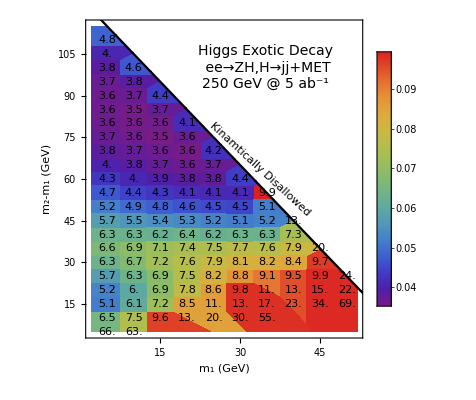

```mathematica
ListDensityPlot[Cases[If[#[[3]]<0.1,{#[[2]],#[[1]]-#[[2]],#[[3]]}]&/@exoticHiggsjjMet95,Except[Null]],PlotLegends->Placed[Automatic,Scaled[{0.92,0.6}]],InterpolationOrder->0,ColorFunction->"Rainbow",PlotRange->{{2,52},{5,115}},BaseStyle->12,FrameLabel->{"m_1 (GeV)","m_2-m_1 (GeV)","95% C.L. Upper limit on Higgs Exo. Br(10^-4)"},FrameStyle->Black];
RegionPlot[2x+y>125,{x,0,125},{y,0,125},PlotStyle->White,BoundaryStyle->Black];
Show[%%,%,Epilog->Flatten[{Flatten[Cases[Table[If[exoticHiggsjjMet95[[i,3]]<1,Inset[NumberForm[100exoticHiggsjjMet95[[i,3]],2],{exoticHiggsjjMet95[[i,2]],exoticHiggsjjMet95[[i,1]]-exoticHiggsjjMet95[[i,2]]}],Null],{i,1,Length[exoticHiggsjjMet95]}],Except[Null]],1],Inset[Rotate["Kinamtically Disallowed",-Pi 0.95/4],Scaled[{0.63,0.53}]],Inset[Style["Higgs Exotic Decay\n ee→ZH,H→jj+MET\n250 GeV @ 5 ab^-1",14],Scaled[{0.65,0.85}]]},1]]
```